```mathematica
SetDirectory[NotebookDirectory[]]
<<mathutils.m
```

/Users/Gautham/Desktop/Robotics Project/Mathematica

```mathematica
(*Kinematic and Dynamic formulation of a planar 6-bar mechanism*)
```

```mathematica
(*Definitions*)
mf[x_]:=MatrixForm[x]
d[x_]:=Dimensions[x]
```

```mathematica
(*Robot*)
```

-Graphics-

```mathematica
(*Robot parameters*)
```

```mathematica
(*link lengths in mm, the radius of the link is taken to be 10mm*)
ldata = {l1->1,r1->0.75,h->2,r2->0.75,l2->1,b->2};
mdata = {m11->π*10^2*l1*0.0027,m12-> π*10^2*r1*0.0027,mb-> π*10^2*h*0.0027,m21-> π*10^2*l2*0.0027,m22-> π*10^2*r2*0.0027};
Idata = {IC11->m11*l1^2/12,IC12->m12*r1^2/12,ICb->mb*h^2/12,IC21->m21*l2^2/12,IC22->m22*r2^2/12};
```

```mathematica
(*The full configuration generalised coordinates*)
```

```mathematica
q = {ϕ1[t],θ3[t],θ1[t],ϕ2[t],θ2[t]};
```

```mathematica
(*Formulating the loop-closure equations*)
```

```mathematica
L1= {l1*Cos[ϕ1[t]],l1*Sin[ϕ1[t]]};
R1 = {r1*Cos[θ3[t]],r1*Sin[θ3[t]]};
H= {h*Cos[θ1[t]],h*Sin[θ1[t]]};
B = {b,0};
L2 = {l2*Cos[ϕ2[t]],l2*Sin[ϕ2[t]]};
R2 = {r2*Cos[θ2[t]],r2*Sin[θ2[t]]};
```

```mathematica
η = L1+R1+H-B-L2-R2;
```

```mathematica
Jηq = D[η,{q}];
```

```mathematica
(*The velocity Jacobians are*)
```

```mathematica
J11 = D[L1/2,{q}];
J12 = D[L1+R1/2,{q}];
Jb = D[L1+R1+H/2,{q}];
J21 = D[B+L2/2,{q}];
J22 = D[B+L2+R2/2,{q}];
```

```mathematica
Jω11 = {{0,0,0,0,0},{0,0,0,0,0},{1,0,0,0,0}};
Jω12 = {{0,0,0,0,0},{0,0,0,0,0},{0,1,0,0,0}};
Jωb   = {{0,0,0,0,0},{0,0,0,0,0},{0,0,1,0,0}};
Jω21 = {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,1,0}};
Jω22 = {{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,1}};
```

```mathematica
(*Moment of Interias of the links*)
```

```mathematica
I11 = {{0,0,0}, {0,0,0}, {0, 0, IC11}};
I12 = {{0,0,0}, {0,0,0}, {0, 0, IC12}};
Ib   = {{0,0,0}, {0,0,0}, {0, 0, ICb}};
I21 = {{0,0,0}, {0,0,0}, {0, 0, IC21}};
I22 = {{0,0,0}, {0,0,0}, {0, 0, IC22}};
```

```mathematica
(*Mass matrix*)
```

```mathematica
M = Simplify[0.5*(m11*Transpose[J11].J11+m12*Transpose[J12].J12+mb*Transpose[Jb].Jb+m21*Transpose[J21].J21+m22*Transpose[J22].J22+Transpose[Jω11].I11.Jω11+Transpose[Jω12].I12.Jω12+Transpose[Jωb].Ib.Jωb+Transpose[Jω21].I21.Jω21+Transpose[Jω22].I22.Jω22)];
```

```mathematica
(*Verification of mass matrix symmetry*)
```

```mathematica
M-Transpose[M]//MatrixForm
```

(0. | 0 | 0. | 0. | 0.
0 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.)

```mathematica
mf[M/.Idata/.mdata/.ldata/.{θ1[t]->0,θ2[t]->2π/3,θ3[t]->π/3,ϕ1[t]-> 1.9360035480852633,ϕ2[t]-> 1.2055891055045298}]
```

(1.30769 | 0.476193 | -0.302939 | 0. | 0.
0.476193 | 0.536771 | 0.318086 | 0. | 0.
-0.302939 | 0.318086 | 1.13097 | 0. | 0.
0. | 0. | 0. | 0.459458 | 0.0751884
0. | 0. | 0. | 0.0751884 | 0.0596412)

```mathematica
(*Computing the C matix from M matrix*)
```

```mathematica
n = Length[q];
tempC = Table[0, {ii, 1,n}, {jj, 1,n}];
For [ii = 1, ii ≤ n, 
For[jj = 1, jj ≤ n,
For[kk = 1, kk≤ n, 
tempC[[ii,jj]] +=1/2*( D[M[[ii,jj]], q[[kk]]] + D[M[[ii,kk]], q[[jj]]] - D[M[[jj, kk]], q[[ii]]])*D[q[[kk]],t] ;
kk++];
jj++];
ii++];
```

```mathematica
Cmat = FullSimplify[tempC];
```

```mathematica
(*Verifying the property of Cmat*)
```

```mathematica
A = FullSimplify[D[M,t]-2*Cmat];
mf[Simplify[A+Transpose[A]]]
```

(0. | 0. | 0. | 0 | 0
0. | 0. | 0. | 0 | 0
0. | 0. | 0. | 0 | 0
0 | 0 | 0 | 0. | 0.
0 | 0 | 0 | 0. | 0.)

```mathematica
(*Potential gradient*)
```

```mathematica
PE = (m11*(L1[[2]]/2)*g+m12*(L1+R1/2)[[2]]*g+mb*(L1+R1+H/2)[[2]]*g+m21*(B+L2/2)[[2]]*g+m22*(B+L2+R2/2)[[2]]*g)/.g->9.806;
```

```mathematica
PE/.Idata/.mdata/.ldata
```

4.15887 Sin[ϕ1[t]]+6.23831 (0.375 Sin[θ3[t]]+Sin[ϕ1[t]])+16.6355 (Sin[θ1[t]]+0.75 Sin[θ3[t]]+Sin[ϕ1[t]])+4.15887 Sin[ϕ2[t]]+6.23831 (0.375 Sin[θ2[t]]+Sin[ϕ2[t]])

```mathematica
G = D[PE,{q}];
```

```mathematica
(*Now formulating the constraint force term*)
```

```mathematica
tempA = Inverse[Jηq.Inverse[M].Transpose[Jηq]/.Idata/.mdata/.ldata];
d[tempA]
```

{2,2}

```mathematica
tempA/.{θ1[t]->0,θ2[t]->2π/3,θ3[t]->π/3,ϕ1[t]-> 1.9360035480852633,ϕ2[t]-> 1.2055891055045298}
```

{{0.163216,-0.0797086},{-0.0797086,0.161026}}

```mathematica
tempB= D[Jηq,t].D[q,t]/.Idata/.mdata/.ldata;
```

```mathematica
(*The unconstrained acceleration*)
```

```mathematica
a = Inverse[M].(0-Cmat.D[q,t]-G);
d[a]
```

{5}

```mathematica
tempD = Jηq.a;
d[tempD]
```

{2}

```mathematica
(*Computing λ*)
```

```mathematica
λ =-tempA.(tempB+tempD);
```

```mathematica
(*From this the constrained Lagrangian term of the RHS will be*)
```

```mathematica
eqnofmRHS = Transpose[Jηq].λ/.Idata/.mdata/.ldata;
d[eqnofmRHS]
```

{5}

```mathematica
eqnofmLHS = M.D[q,{t,2}]+Cmat.D[q,t]+G/.Idata/.mdata/.ldata;
d[eqnofmLHS]
```

{5}

```mathematica
(*Therefore the complete equation of motion is*)
```

```mathematica
eqnofm = eqnofmLHS-eqnofmRHS;
d[eqnofm]
Variables[eqnofm]
```

{5}

{Cos[θ1[t]],Cos[θ2[t]],Cos[θ1[t]-θ3[t]],Cos[θ3[t]],Cos[θ1[t]-ϕ1[t]],Cos[θ3[t]-ϕ1[t]],Cos[ϕ1[t]],Cos[θ2[t]-ϕ2[t]],Cos[ϕ2[t]],Sin[θ1[t]],Sin[θ2[t]],Sin[θ1[t]-θ3[t]],Sin[θ3[t]],Sin[θ1[t]-ϕ1[t]],Sin[θ3[t]-ϕ1[t]],Sin[ϕ1[t]],Sin[θ2[t]-ϕ2[t]],Sin[ϕ2[t]],θ1'[t],θ2'[t],θ3'[t],ϕ1'[t],ϕ2'[t],θ1''[t],θ2''[t],θ3''[t],ϕ1''[t],ϕ2''[t]}

```mathematica
Jηϕ = D[η,{{ϕ1[t],ϕ2[t]}}]/.ldata
```

{{-Sin[ϕ1[t]],Sin[ϕ2[t]]},{Cos[ϕ1[t]],-Cos[ϕ2[t]]}}

```mathematica
Jηθ = D[η,{{θ1[t],θ2[t],θ3[t]}}]/.ldata
```

{{-2 Sin[θ1[t]],0.75 Sin[θ2[t]],-0.75 Sin[θ3[t]]},{2 Cos[θ1[t]],-0.75 Cos[θ2[t]],0.75 Cos[θ3[t]]}}

```mathematica
Jϕθ = Inverse[Jηϕ].Jηθ/.ldata;
```

```mathematica
Jqθ = {Jϕθ[[1]],{0,0,1},{1,0,0},Jϕθ[[2]],{0,1,0}};
```

```mathematica
Mθ=(Transpose[Jqθ].M.Jqθ)/.Idata/.mdata/.ldata;
```

```mathematica
Dimensions[Mθ]
```

{3,3}

```mathematica
Cθ = Transpose[Jqθ].(M.D[Jqθ,t]+Cmat.Jqθ);
```

```mathematica
Dimensions[Cθ]
```

{3,3}

```mathematica
Chop[Simplify[Transpose[Mθ]-Mθ]]
```

{{0,0.,0.},{0.,0,0},{0.,0,0}}

```mathematica
(*A = FullSimplify[D[Mθ,t]-2*Cθ];*)
```

```mathematica
qth = {θ1[t],θ2[t],θ3[t]};
```

```mathematica
u = Mθ.D[qth,{t,2}]+Cθ.D[qth,t];
```

```mathematica
Dimensions[u]
```

{3}

```mathematica
Obj = Norm[u]/.Idata/.mdata/.ldata;
```

```mathematica
(*Interpolating the actuator states with a sixt order polynomial*)
```

```mathematica
inter[t] = a0+a1*t^1+a2*t^2+a3*t^3+a4*t^4+a5*t^5
```

a0+a1 t+a2 t^2+a3 t^3+a4 t^4+a5 t^5

```mathematica
solpar = Solve[{(inter[t]/.t->0)==θi,(inter[t]/.t->tf)==θf,(D[inter[t],t]/.t->0)==0,(D[inter[t],t]/.t->tf)==0},{a0,a1,a2,a3}]
```

{{a0→θi,a1→0,a2→-(-a4 tf^4-2 a5 tf^5-3 θf+3 θi)/tf^2,a3→-(2 a4 tf^4+3 a5 tf^5+2 θf-2 θi)/tf^3}}

```mathematica
θinter = Together[Simplify[inter[t]/.solpar]]
```

{1/tf^3(a4 t^4 tf^3+a5 t^5 tf^3-2 a4 t^3 tf^4+a4 t^2 tf^5-3 a5 t^3 tf^5+2 a5 t^2 tf^6-2 t^3 θf+3 t^2 tf θf+2 t^3 θi-3 t^2 tf θi+tf^3 θi)}

```mathematica
Variables[θinter]
```

{a4,a5,t,tf,θf,θi}

```mathematica
θ1inter = θinter/.{θf->θ1f,θi->θ1i}
```

{1/tf^3(a4 t^4 tf^3+a5 t^5 tf^3-2 a4 t^3 tf^4+a4 t^2 tf^5-3 a5 t^3 tf^5+2 a5 t^2 tf^6-2 t^3 θ1f+3 t^2 tf θ1f+2 t^3 θ1i-3 t^2 tf θ1i+tf^3 θ1i)}

```mathematica
θ2inter = θinter/.{a4->b4,a5->b5,θf->θ2f,θi->θ2i}
```

{1/tf^3(b4 t^4 tf^3+b5 t^5 tf^3-2 b4 t^3 tf^4+b4 t^2 tf^5-3 b5 t^3 tf^5+2 b5 t^2 tf^6-2 t^3 θ2f+3 t^2 tf θ2f+2 t^3 θ2i-3 t^2 tf θ2i+tf^3 θ2i)}

```mathematica
Variables[θ2inter]
```

{b4,b5,t,tf,θ2f,θ2i}

```mathematica
θ3inter = θinter/.{a4->c4,a5->c5,a6->c6,θf->θ3f,θi->θ3i}
```

{1/tf^3(c4 t^4 tf^3+c5 t^5 tf^3-2 c4 t^3 tf^4+c4 t^2 tf^5-3 c5 t^3 tf^5+2 c5 t^2 tf^6-2 t^3 θ3f+3 t^2 tf θ3f+2 t^3 θ3i-3 t^2 tf θ3i+tf^3 θ3i)}

```mathematica
Variables[θ3inter]
```

{c4,c5,t,tf,θ3f,θ3i}

```mathematica
θ1interval = θ1inter/.tf->2/.θ1i->0/.θ1f->0
```

{1/8 (32 a4 t^2+128 a5 t^2-32 a4 t^3-96 a5 t^3+8 a4 t^4+8 a5 t^5)}

```mathematica
θ2interval = θ2inter/.tf->2/.θ2i->0/.θ2f->π/3
```

{1/8 (32 b4 t^2+128 b5 t^2+2 π t^2-32 b4 t^3-96 b5 t^3-(2 π t^3)/3+8 b4 t^4+8 b5 t^5)}

```mathematica
θ3interval = θ3inter/.tf->2/.θ3i->π/.θ3f->2*π/3
```

{1/8 (8 π+32 c4 t^2+128 c5 t^2-2 π t^2-32 c4 t^3-96 c5 t^3+(2 π t^3)/3+8 c4 t^4+8 c5 t^5)}

```mathematica
(*parameterizing the Objective*)
```

```mathematica
Objpara = Obj/.{θ1[t]->θ1interval,θ2[t]->θ2interval,θ3[t]->θ3interval,θ1'[t]->D[θ1interval,t],θ2'[t]->D[θ2interval,t],θ3'[t]->D[θ3interval,t],θ1''[t]->D[θ1interval,{t,2}],θ2''[t]->D[θ2interval,{t,2}],θ3''[t]->D[θ3interval,{t,2}]};
```

```mathematica
(*FK for replacing all ϕ's in terms of θ's*)
```

```mathematica
η2=( l1*Sin[ϕ1[t]]+r1*Sin[θ3[t]]+h*Sin[θ1[t]]-(l1*Sin[ϕ2[t]]+r1*Sin[θ2[t]]));
```

```mathematica
η1 =( l1*Cos[ϕ1[t]]+r1*Cos[θ3[t]]+h*Cos[θ1[t]]-(l1*Cos[ϕ2[t]]+r1*Cos[θ2[t]]+b));
```

```mathematica
ee3 = Numerator[Together[solveLinTrig2[{η1,η2},ϕ2[t]][[2]]/.{Cos[ϕ1[t]]-> (1-p^2)/(1+p^2),Sin[ϕ1[t]]-> (2*p)/(1+p^2)}]];
```

```mathematica
et=Solve[ee3==0,p][[2]];
Dimensions[et]
```

{1}

```mathematica
Clear[ϕ1sol]
```

```mathematica
ϕ1sol ={ϕ1[t]->  ArcTan[(1-p^2)/(1+p^2),(2*p)/(1+p^2)]/.et}/.ldata;
```

```mathematica
ϕ2sol = solveLinTrig2[{η1,η2},ϕ2[t]][[1]]/.ϕ1sol/.ldata;
```

```mathematica
ϕ1solp = (ϕ1[t]/.ϕ1sol)/.{θ1[t]->θ1interval,θ2[t]->θ2interval,θ3[t]->θ3interval,θ1'[t]->D[θ1interval,t],θ2'[t]->D[θ2interval,t],θ3'[t]->D[θ3interval,t],θ1''[t]->D[θ1interval,{t,2}],θ2''[t]->D[θ2interval,{t,2}],θ3''[t]->D[θ3interval,{t,2}]};
```

```mathematica
ϕ2solp = (ϕ2[t]/.ϕ2sol)/.{θ1[t]->θ1interval,θ2[t]->θ2interval,θ3[t]->θ3interval,θ1'[t]->D[θ1interval,t],θ2'[t]->D[θ2interval,t],θ3'[t]->D[θ3interval,t],θ1''[t]->D[θ1interval,{t,2}],θ2''[t]->D[θ2interval,{t,2}],θ3''[t]->D[θ3interval,{t,2}]};
```

```mathematica
dϕ1solp = D[ϕ1solp,t];
```

```mathematica
dϕ2solp = D[ϕ2solp,t];
```

```mathematica
Variables[dϕ2solp]
```

{a4,a5,b4,b5,c4,c5,t,Cos[1/8 (32 a4 t^2+128 a5 t^2-32 a4 t^3-96 a5 t^3+8 a4 t^4+8 a5 t^5)],Cos[1/8 (32 b4 t^2+128 b5 t^2+2 π t^2-32 b4 t^3-96 b5 t^3-(2 π t^3)/3+8 b4 t^4+8 b5 t^5)],Cos[1/8 (8 π+32 c4 t^2+128 c5 t^2-2 π t^2-32 c4 t^3-96 c5 t^3+(2 π t^3)/3+8 c4 t^4+8 c5 t^5)],Sin[1/8 (32 a4 t^2+128 a5 t^2-32 a4 t^3-96 a5 t^3+8 a4 t^4+8 a5 t^5)],Sin[1/8 (32 b4 t^2+128 b5 t^2+2 π t^2-32 b4 t^3-96 b5 t^3-(2 π t^3)/3+8 b4 t^4+8 b5 t^5)],Sin[1/8 (8 π+32 c4 t^2+128 c5 t^2-2 π t^2-32 c4 t^3-96 c5 t^3+(2 π t^3)/3+8 c4 t^4+8 c5 t^5)]}

```mathematica
Objfullpara = Objpara/.{ϕ1[t]->ϕ1solp,ϕ2[t]->ϕ2solp,ϕ1'[t]->dϕ1solp,ϕ2'[t]->dϕ2solp};
```

```mathematica
(*temp = NMinimize[(Abs[Objfullpara[[1]][[1]]]/.{t->1}),
{a4,a5,a6,b4,b5,b6,c4,c5,c6}]*)
```

```mathematica
(*GaussInteg  =
  ((0.568889)*Objfullpara[[1]][[1]]/.{t-> 1})+((0.478629)*Objfullpara[[1]][[1]]/.{t-> 1.538469})+((0.478629)*Objfullpara[[1]][[1]]/.{t-> 0.461531})+((0.236927)*Objfullpara[[1]][[1]]/.{t-> 1.90618})+((0.236927)*Objfullpara[[1]][[1]]/.{t->0.09382});*)
```

```mathematica
(*Formulation of the Gauss Integration at 2,3,5 points*)
```

```mathematica
Clear[GaussInteg]
```

```mathematica
GaussInteg  =
0.888889*(Flatten[Objfullpara]/.{t-> 1})[[1]]+0.55556*(Flatten[Objfullpara]/.{t->1.774597})[[1]]+0.55556*(Flatten[Objfullpara]/.{t->0.225403})[[1]];(*0.236927*(Flatten[Objfullpara]/.{t-> 1.90618})[[1]]+0.236927*(Flatten[Objfullpara]/.{t-> 0.09382})[[1]]*)
```

```mathematica
(*NMinimize[Abs[GaussInteg],
{a4,b4,c4}]*)
```

```mathematica
(*{0.0002532122826116134,{a4->0.34004238436918915,a5->-0.15971751549983393,a6->0.16415872254960695,b4->-0.20517344890560835,b5->0.24723944476462087,b6->-0.28657760193011095,c4->0.45983693080481486,c5->-0.11235563532705237,c6->-0.006768291561819116}}*)
```

```mathematica
(*Save["Gauss",GaussInteg]*)
```

```mathematica
NotebookDirectory[]
```

/Users/Gautham/Desktop/Robotics Project/Mathematica/

```mathematica
θ1tra=(θ1interval/.{a4->0.34004238436918915,a5->-0.15971751549983393,a6->0.16415872254960695,b4->-0.20517344890560835,b5->0.24723944476462087,b6->-0.28657760193011095,c4->0.45983693080481486,c5->-0.11235563532705237,c6->-0.006768291561819116})[[1]]
```

1/8 (53.4745 t^2-37.5731 t^3+2.72034 t^4-1.27774 t^5+1.31327 t^6)

```mathematica
θ2tra=(θ2interval/.{a4->0.34004238436918915,a5->-0.15971751549983393,a6->0.16415872254960695,b4->-0.20517344890560835,b5->0.24723944476462087,b6->-0.28657760193011095,c4->0.45983693080481486,c5->-0.11235563532705237,c6->-0.006768291561819116})[[1]]
```

1/8 (-72.3983 t^2+52.0056 t^3-1.64139 t^4+1.97792 t^5-2.29262 t^6)

```mathematica
θ3tra=(N[θ3interval/.{a4->0.34004238436918915,a5->-0.15971751549983393,a6->0.16415872254960695,b4->-0.20517344890560835,b5->0.24723944476462087,b6->-0.28657760193011095,c4->0.45983693080481486,c5->-0.11235563532705237,c6->-0.006768291561819116}])[[1]]
```

0.125 (25.1327-14.6905 t^2+1.94563 t^3+3.6787 t^4-0.898845 t^5-0.0541463 t^6)

```mathematica
th1opt = {};
th2opt = {};
th3opt = {};
For[i=1,i≤ 1000,i++,
AppendTo[th1opt,θ1tra/.{t-> (2*i)/1000}];
AppendTo[th2opt,θ2tra/.{t-> (2*i)/1000}];
AppendTo[th3opt,θ3tra/.{t-> (2*i)/1000}];

]
```

```mathematica
(*Plotting the solution*)
```

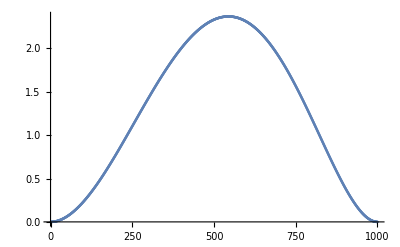

```mathematica
ListPlot[th1opt]
```

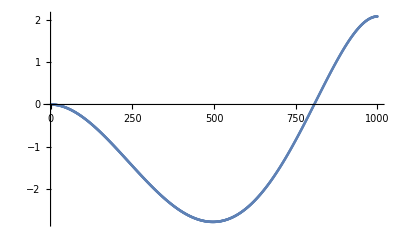

```mathematica
ListPlot[th2opt]
```

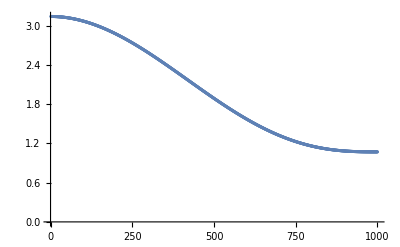

```mathematica
ListPlot[th3opt]
```

```mathematica
(*Module to give ϕ's at a pose given θ's*)
```

```mathematica
θtoϕ[a_,b_,c_]:=
Module[{l1,l2,θ1,θ2,θ3,l3,η1,η2,ee3,data,t,ϕ1sol,ϕ2sol,η11,η12,et},
l1 = 1;
l2 = 0.75;
l3 = 2;
θ1 = a;θ2=b;θ3=c;
η2=( l1*Sin[ϕ1]+l2*Sin[θ3]+l3*Sin[θ1]-(l1*Sin[ϕ2]+l2*Sin[θ2]));
η1 =( l1*Cos[ϕ1]+l2*Cos[θ3]+l3*Cos[θ1]-(l1*Cos[ϕ2]+l2*Cos[θ2]+l3));
ee3 = Numerator[Together[solveLinTrig2[{η1,η2},ϕ2][[2]]/.{Cos[ϕ1]-> (1-t^2)/(1+t^2),Sin[ϕ1]-> (2*t)/(1+t^2)}]];
et=Solve[ee3==0,t][[2]];
ϕ1sol ={ϕ1->  ArcTan[(1-t^2)/(1+t^2),(2*t)/(1+t^2)]/.et};
η11=η1/.ϕ1sol;
η12=η2/.ϕ1sol;
ϕ2sol = solveLinTrig2[{η11,η12},ϕ2][[1]];
Return[Flatten[{ϕ1sol,ϕ2sol}]];
]
```

```mathematica
ϕllist = {};
ϕ2list = {};
For[i=1,i≤ 1000,i++,
AppendTo[ϕlist,ϕ1/.θtoϕ[th1opt[[i]],th3opt[[i]],th2opt[[i]]]]

AppendTo[ϕ2ist,ϕ2/.θtoϕ[th1opt[[i]],th3opt[[i]],th2opt[[i]]]]

]
```

```mathematica
Export["th1opt.csv",th1opt];
Export["th2opt.csv",th2opt];
Export["th3opt.csv",th3opt];
```

```mathematica
i=150;
ϕ2/.θtoϕ[th1opt[[i]],th3opt[[i]],th2opt[[i]]]
```

1.25052

```mathematica
Clear[omnama]
```

```mathematica
(*SetOptions[Simplify,TimeConstraint->700];*)
omnama=NMinimize[{GaussInteg^2},{a4,a5,b4,b5,c4,c5}]
```

{0.112064,{a4→0.234236,a5→-0.0398042,b4→-1.98131,b5→0.515957,c4→3.60944,c5→-0.746929}}

```mathematica
(*{2.1254211384160744,{a4->0.02070444737030495,b4->0.20691222069452203,c4->0.0198771778340989}}*)
```

```mathematica
(*{0.03136038045840917,{a4->-0.2646641347804604,b4->1.5280915964749295,c4->0.7573311315045893}}*)
```

```mathematica
θ1opt = θ1interval/.omnama[[2]]
```

{1/8 (2.40062 t^2-3.67435 t^3+1.87389 t^4-0.318433 t^5)}

```mathematica
θ2opt = θ2interval/.omnama[[2]]
```

{1/8 (8.92371 t^2+11.7757 t^3-15.8505 t^4+4.12766 t^5)}

```mathematica
θ3opt = θ3interval/.omnama[[2]]
```

{1/8 (8 π+13.6118 t^2-41.7024 t^3+28.8755 t^4-5.97544 t^5)}

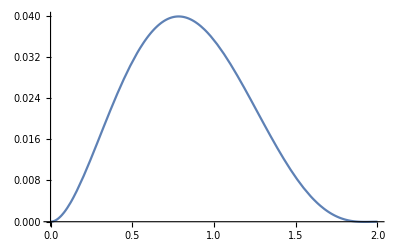

```mathematica
Plot[θ1opt[[1]],{t,0,2}]
```

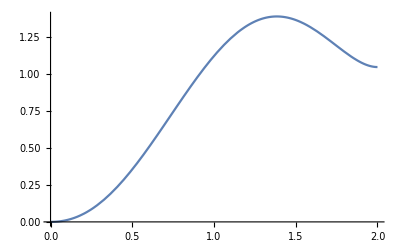

```mathematica
Plot[θ2opt[[1]],{t,0,2}]
```

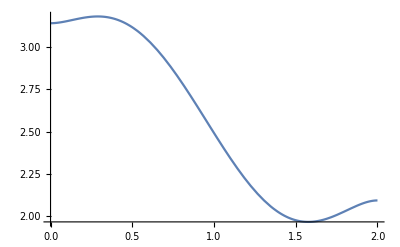

```mathematica
Plot[θ3opt[[1]],{t,0,2}]
```

```mathematica
ϕ1list = ConstantArray[0,1000];
ϕ2list = ConstantArray[0,1000];
θ2list = ConstantArray[0,1000];
θ1list = ConstantArray[0,1000];
θ3list = ConstantArray[0,1000];
```

```mathematica
For[i=1,i≤ 1000,i++,
θ1list[[i]] = (θ1opt/.(t->2*i/1000))[[1]];
θ2list[[i]] = (θ2opt/.(t->2*i/1000))[[1]];
θ3list[[i]] = (θ3opt/.(t->2*i/1000))[[1]];
ϕ1list[[i]] = ϕ1/.θtoϕ[θ1list[[i]],θ2list[[i]],θ3list[[i]]];
ϕ2list[[i]] = ϕ2/.θtoϕ[θ1list[[i]],θ2list[[i]],θ3list[[i]]];
];
```

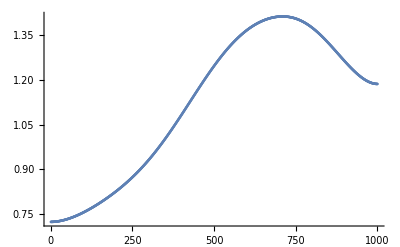

```mathematica
ListPlot[ϕ1list]
```

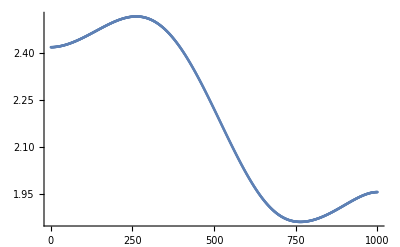

```mathematica
ListPlot[ϕ2list]
```

```mathematica
Export["th3god2.csv",θ3list];
Export["th2god2.csv",θ2list];
Export["th1god2.csv",θ1list];
Export["ph1god2.csv",ϕ1list];
Export["ph2god2.csv",ϕ2list];
```

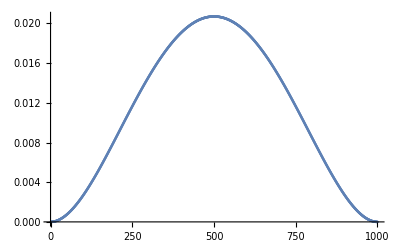

```mathematica
ListPlot[θ1list]
```

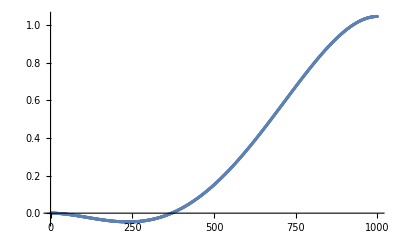

```mathematica
ListPlot[θ2list]
```

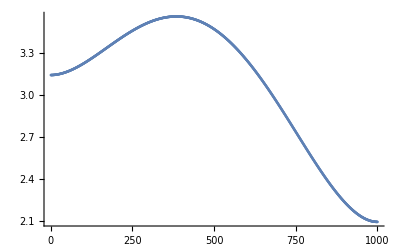

```mathematica
ListPlot[θ3list]
```